# 二维第一个子集 只显示和

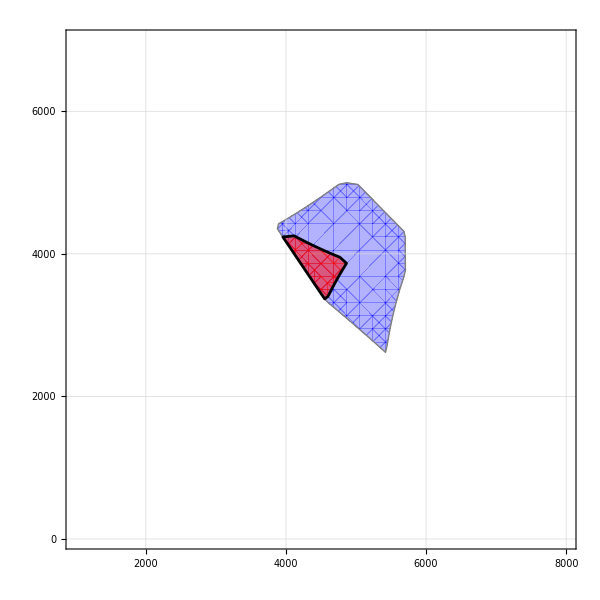

./ee10.pdf

```mathematica
x1=f1;
x2=f2;
x3=10000-f1-f2;
x5=10000-f1-f2;
x8=10000-f1-f2;
e=10;
rho=15;
sigma=0.02;

link1=18*(1+0.15*(x1/3600)^4);
link2=22.5*(1+0.15*(x2/3600)^4);
link3=12*(1+0.15*(x3/1800)^4);
link5=2.4*(1+0.15*(x5/1800)^4);
link8=12*(1+0.15*(x8/1800)^4);

path1=link1+rho*(1-Exp[-sigma*link1]);
path2=link2+rho*(1-Exp[-sigma*link2]);
path5=link3+link5+link8+rho*(1-Exp[-sigma*(link3+link5+link8)]);

m1=20;
m2=15;
m5=2;

p1=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&(path1-path2)*(m1-m2)<0&&(path1-path5)*(m1-m5)<0&&(path2-path5)*(m2-m5)<0&&10000-f1-f2>=0,{f1,1000,8000},{f2,0,7000},Axes->True,Mesh->None,BoundaryStyle->Black,PlotStyle->Directive[Red,Opacity[0.5]],Frame->True,FrameTicksStyle->Directive[Black,FontSize->24],GridLines->Automatic,GridLinesStyle->LightGray,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{Style["Subscript[f, 1]",32],Style["Subscript[f, 2]",32]}];

p2=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&f1+f2<=10000,{f1,1000,8000},{f2,0,7000},Axes->True,Mesh->None,BoundaryStyle->{Thick,Gray},PlotStyle->Directive[Blue,Opacity[0.3]],Frame->True,FrameTicksStyle->Directive[Black,FontSize->24],GridLines->Automatic,GridLinesStyle->LightGray,FrameTicks->{{All, None},{All,None}},FrameLabel->{Style["",32],Style["",32]}];

Show[p2,p1,ImageSize->600]
Export["./ee"<>ToString[e]<>".pdf",Show[p2,p1,ImageSize->600]]
```

```mathematica
|
```

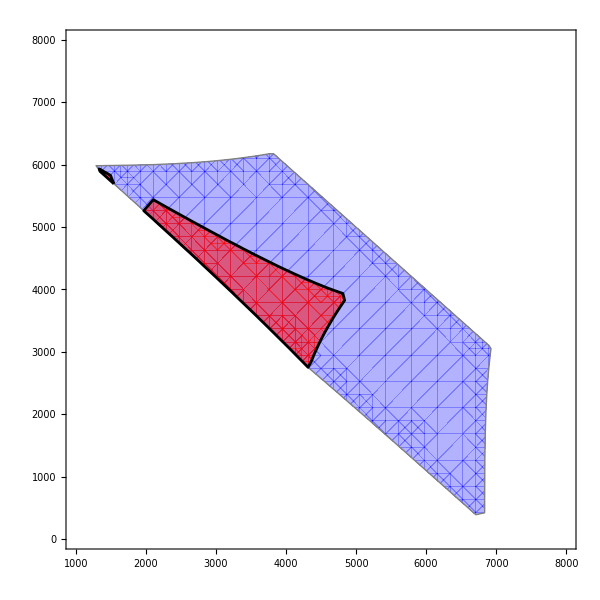

# 三维 第一个子集 只显示和

```mathematica
lft[t0_,x_,c_]:=t0 (1+0.15 (x/c)^4)
zeta=15;

pt1[f1_]:=lft[18,f1,3600];
pt2[f2_]:=lft[22.5,f2,3600];
pt5[f5_]:=2*lft[12,f5,1800]+lft[2.4,f5,1800];
 max[f1_,f2_,f5_] = Max[pt1[f1],pt2[f2],pt5[f5]];
 min[f1_,f2_,f5_] = Min[pt1[f1],pt2[f2],pt5[f5]];
m1 = 20;
m2 = 15;
m5 = 2;
p1=ParametricPlot3D[{u,v,10000-u-v},{u,1000,10000},{v,1000,10000},RegionFunction->Function[{u,v,f5},max[u,v,f5]-min[u,v,f5]<=zeta],PlotPoints->220,Mesh->None,AxesLabel->{"f1","f2","f5"},PlotLabel->"Feasible region on f1 + f2 + f5 = 10000",PlotStyle->Opacity[0.6,Blue]];

p2=ParametricPlot3D[{u,v,10000-u-v},{u,1000,10000},{v,1000,10000},RegionFunction->Function[{u,v,f5},max[u,v,f5]-min[u,v,f5]<zeta && pt1[u] <=pt2[v]&&pt2[v]<= pt5[f5]],PlotPoints->200,Mesh->None,AxesLabel->{"f1","f2","f5"},PlotLabel->"Feasible region on f1 + f2 + f5 = 10000",PlotStyle->Opacity[0.6,Red]];
Show[p2,p1]
```

-Graphics3D-

# 三维 第二个子集，显示 , 可接受路径集

```mathematica
ClearAll[lft,costs];
lft[c_,f_,denom_]:=c (1+0.15 (f/denom)^4);

total=10^4;
regionConstraint[{f1_,f2_,f5_},α_,ζ_]:=Module[{s=total-f1-f2-f5,f3,f4,pts},If[s<0,Return[False]];(*必须显式写 s≥0*)f3=α s;
f4=(1-α) s;
pts={lft[18,f1,3600],lft[22.5,f2,3600],lft[12,f3+f5,1800]+lft[24,f3,1800],lft[24,f4,1800]+lft[12,f4+f5,1800],lft[12,f3+f5,1800]+lft[2.4,f5,1800]+lft[12,f4+f5,1800]};
Max[pts]-Min[pts]<=ζ              (*成本波动约束*)];

Manipulate[
RegionPlot3D[
regionConstraint[{f1,f2,f5},α,ζ],
{f1,3000,6100},{f2,1200,6100},{f5,0,2200},
(*关键改动↓↓↓*)
PlotPoints->60,(*更高分辨率*)
MaxRecursion->2,(*自动再细分边界*)
WorkingPrecision->50,(*提升数值精度，避免漏采样*)
EvaluationMonitor:>Sow[{f1,f2,f5}],(*可视化采样点时调试*)
PlotStyle->Directive[Opacity[0.9],Darker[Green,0.2]],
BoundaryStyle->None,
Mesh->None,
AxesLabel->(Style[#,14,Bold]&/@{"f₁","f₂","f₅"}),
Boxed->False,Lighting->"Neutral"],
{{α,0.5,Style["α  (f₃ : f₄)",11]},0,1},
{{ζ,15,Style["ζ  (成本差上限)",11]},0,100},
ControlPlacement->Left,TrackedSymbols:>{α,ζ}
]
```

RegionPlot3D::boolf: regionConstraint[{f1, f2, f5}, 0.5, 15] 必须是一个 Boolean 函数.

General::stop: 在本次计算中，RegionPlot3D::boolf 的进一步输出将被抑制.

# 三维 第二个子集，显示 , 双目标可接受路径集

```mathematica
(*──────────────── 0. 公共函数与参数 ────────────────*)(*{f1,3000,6100},{f2,1200,6100},{f5,0,2200},*)
ClearAll[lft,costList];
lft[c_,f_,denom_]:=c (1+0.15 (f/denom)^4);

total=10^4;                 (*流量总量*)
αFix=0.5;                  (*f3:f4 分配比例*)
ζFix=15;                   (*成本最大波动*)

(*计算五条路径成本*)
costList[{f1_,f2_,f5_},α_]:=Module[{s,f3,f4},
s=total-f1-f2-f5;
If[s<0,Return[$Failed]];(*质量守恒不满足直接剔除*)
f3=α s;
f4=(1-α) s;
{lft[18,f1,3600],(*pt1*)
lft[22.5,f2,3600],(*pt2*)
lft[12,f3+f5,1800]+lft[24,f3,1800],(*pt3*)
lft[24,f4,1800]+lft[12,f4+f5,1800],(*pt4*)
lft[12,f3+f5,1800]+lft[2.4,f5,1800]+lft[12,f4+f5,1800]}(*pt5*)
];

(*──────────────── 1. 原始可行域 ────────────────*)
origRegionPlot=RegionPlot3D[
With[{pts=costList[{f1,f2,f5},αFix]},
If[pts===$Failed,False,Max[pts]-Min[pts]<=ζFix          (*仅成本差约束*)]
],
{f1,4000,7000},{f2,1500,6000},{f5,0,2500},
PlotPoints->60,
MaxRecursion->15,
WorkingPrecision->50,
Mesh->None,
PlotStyle->Directive[Opacity[0.25],ColorData["TemperatureMap"][#3]&],
BoundaryStyle->None];

(*──────────────── 2. 强化可行域（新增次序约束） ────────────────*)
strongRegionPlot=RegionPlot3D[
With[{pts=costList[{f1,f2,f5},αFix]},
If[pts===$Failed,False,
Max[pts]-Min[pts]<=ζFix&&(*原约束*)
pts[[3]]>pts[[5]]&&(*pt3>pt5*)
pts[[4]]>pts[[5]]&&(*pt4>pt5*)
pts[[5]]>pts[[2]]&&(*pt5>pt2*)
pts[[2]]>pts[[1]](*pt2>pt1*)]
],
{f1,3000,5000},{f2,2000,5000},{f5,0,2500},
PlotPoints->60,
MaxRecursion->15,
WorkingPrecision->50,
Mesh->None,
PlotStyle->Directive[Opacity[0.85],Darker[Red,0.1]],
BoundaryStyle->None];

(*──────────────── 3. 合并显示 ────────────────*)
Show[
origRegionPlot,(*透明青色->原可行域*)
strongRegionPlot,(*深红->强化区域*)
Boxed->False,
Axes->True,
AxesLabel->(Style[#,14,Bold]&/@{"f₁","f₂","f₅"}),
Lighting->"Neutral",
PlotRange->Automatic,
ImageSize->Large
]
```

-Graphics3D-

```mathematica
Show[%80,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Export["/Users/jinghong/Documents/Code/Python_BRUE/1.ply",%81,"PLY"]
```

/Users/jinghong/Documents/Code/Python_BRUE/1.ply

```mathematica
Rasterize[%81,"Image"]
```

# 生成六个图

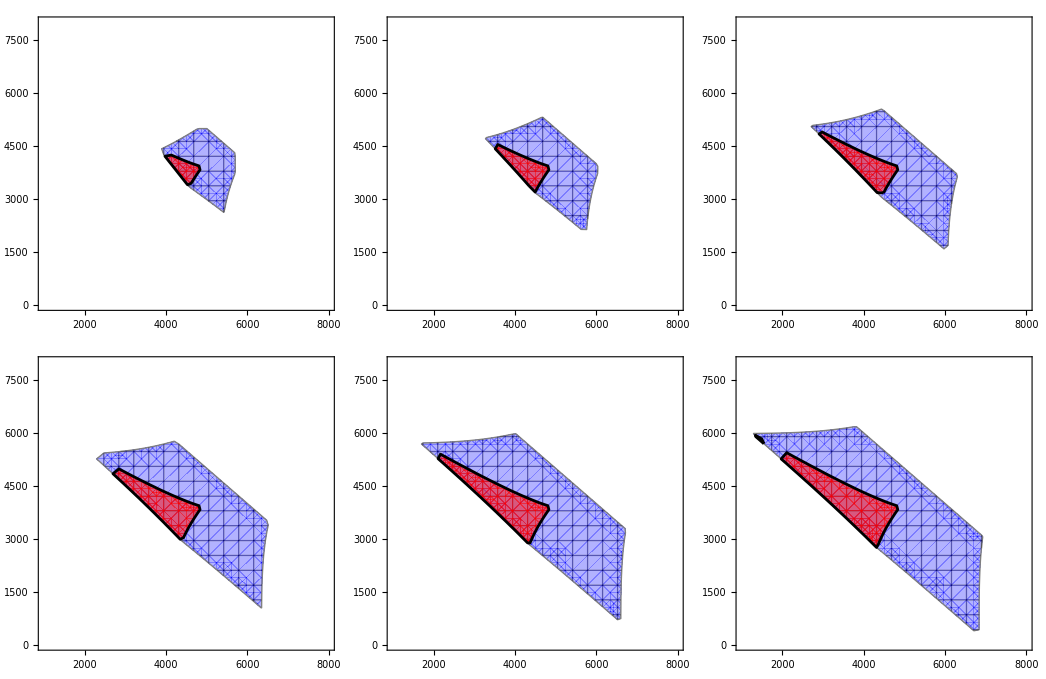

```mathematica
ClearAll[f1,f2,pathPlot]
pathPlot[e_]:=Module[{x1,x2,x3,x5,x8,rho,sigma,link1,link2,link3,link5,link8,path1,path2,path5,m1,m2,m5,p1,p2},rho=15;
sigma=0.02;
m1=20;
m2=15;
m5=2;
x1=f1;
x2=f2;
x3=10000-f1-f2;
x5=x3;
x8=x3;
link1=18*(1+0.15*(x1/3600)^4);
link2=22.5*(1+0.15*(x2/3600)^4);
link3=12*(1+0.15*(x3/1800)^4);
link5=2.4*(1+0.15*(x5/1800)^4);
link8=12*(1+0.15*(x8/1800)^4);
path1=link1+rho*(1-Exp[-sigma*link1]);
path2=link2+rho*(1-Exp[-sigma*link2]);
path5=link3+link5+link8+rho*(1-Exp[-sigma*(link3+link5+link8)]);
p1=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&(path1-path2)*(m1-m2)<0&&(path1-path5)*(m1-m5)<0&&(path2-path5)*(m2-m5)<0&&10000-f1-f2>=0,{f1,1000,8000},{f2,0,8000},Axes->True,Mesh->None,BoundaryStyle->Black,PlotStyle->Directive[Red,Opacity[0.5]],FrameTicksStyle->Directive[Black,FontSize->12],FrameLabel->{Style["",18],Style["",18]},PlotLegends->None];
p2=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&f1+f2<=10000,{f1,1000,8000},{f2,0,8000},Axes->True,Mesh->Full,BoundaryStyle->{Thick,Gray},PlotStyle->Directive[Blue,Opacity[0.3]],FrameTicksStyle->Directive[Black,FontSize->12],FrameLabel->{Style["",18],Style["",18]},PlotLegends->None];
Show[p2,p1,ImageSize->Large]]

plots=Map[pathPlot,{10,15,20,25,30,35}];

legend=SwatchLegend[{Blue,Red},{"Feasible Region","Nash Equilibrium Region"},LegendMarkers->{"Rectangle","Rectangle"},LegendLayout->"Row",LabelStyle->Directive[FontSize->14]];

finalPlot=GraphicsGrid[Partition[plots,3],Spacings->{1,1},Dividers->None,Frame->None,ImageSize->Large];
combined=Labeled[finalPlot,legend,Bottom]
```

# p1和p2区域内随机生成点并在图上显示

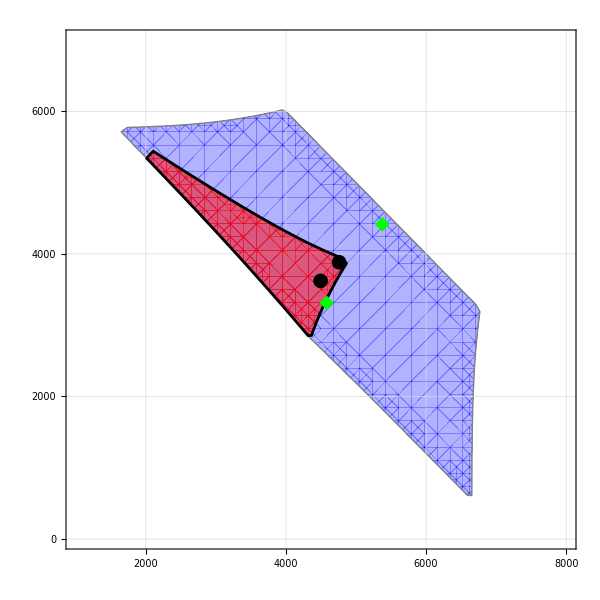

./ee_point31.pdf

```mathematica
x1=f1;
x2=f2;
x3=10000-f1-f2;
x5=10000-f1-f2;
x8=10000-f1-f2;
e=15;
rho=15;
sigma=0.02;

link1=18*(1+0.15*(x1/3600)^4);
link2=22.5*(1+0.15*(x2/3600)^4);
link3=12*(1+0.15*(x3/1800)^4);
link5=2.4*(1+0.15*(x5/1800)^4);
link8=12*(1+0.15*(x8/1800)^4);

path1=link1+rho*(1-Exp[-sigma*link1]);
path2=link2+rho*(1-Exp[-sigma*link2]);
path5=link3+link5+link8+rho*(1-Exp[-sigma*(link3+link5+link8)]);

m1=20;
m2=15;
m5=2;

p1=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&(path1-path2)*(m1-m2)<0&&(path1-path5)*(m1-m5)<0&&(path2-path5)*(m2-m5)<0&&10000-f1-f2>=0,{f1,1000,8000},{f2,0,7000},Axes->True,Mesh->None,BoundaryStyle->Black,PlotStyle->Directive[Red,Opacity[0.5]],Frame->True,FrameTicksStyle->Directive[Black,FontSize->24],GridLines->Automatic,GridLinesStyle->LightGray,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{Style["Subscript[f, 1]",32],Style["Subscript[f, 2]",32]}];

p2=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&f1+f2<=10000,{f1,1000,8000},{f2,0,7000},Axes->True,Mesh->None,BoundaryStyle->{Thick,Gray},PlotStyle->Directive[Blue,Opacity[0.3]],Frame->True,FrameTicksStyle->Directive[Black,FontSize->24],GridLines->Automatic,GridLinesStyle->LightGray,FrameTicks->{{All,None},{All,None}}];

(*定义流量方案点*)
pathConstraintPoints={{5373.80,4413.76},{4582.07,3312.18}};
allConstraintPoints={{4758.09,3882.45},{4493.79,3621.15}};

(*创建满足全部约束的流量方案点的图*)
p3=ListPlot[allConstraintPoints,PlotStyle->{PointSize[0.02],Black},PlotMarkers->{"●",15},PlotLegends->None];

(*创建只满足路径约束的流量方案点的图*)
p4=ListPlot[pathConstraintPoints,PlotStyle->{PointSize[0.02],Green},PlotMarkers->{"◆",15},PlotLegends->None];

Show[p2,p1,p3,p4,ImageSize->600]
Export["./ee_point"<>ToString[e]<>".pdf",Show[p2,p1,p3,p4,ImageSize->600]]
```

# 时间盈余

约束全部满足？  False

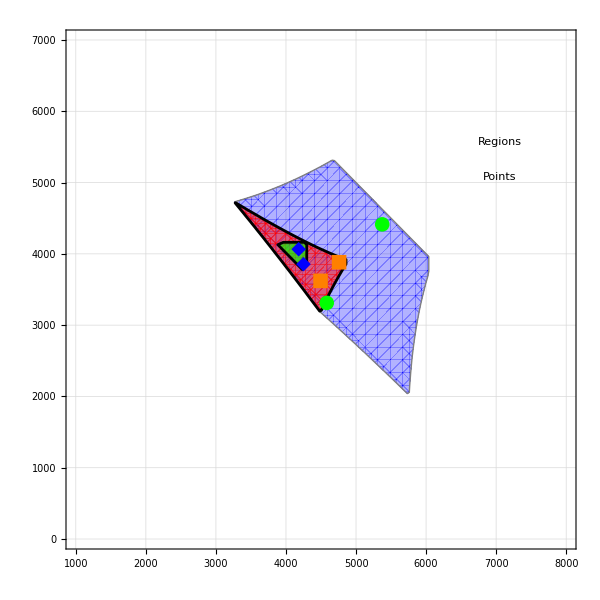

```mathematica
(* ========================基本定义========================*)ClearAll[f1,f2,link1,link2,link3,link5,link8,path1,path2,path5,maxPath,minPath,r1,r2,r5,midPath1,midPath2,midPath5,reg,reg2,reg3,order,pair,box,cons2,eps,e,rho,sigma,m1,m2,m5,seeds];

(*常数*)
rho=15.;
sigma=0.02;
e=15.;
eps=1.*^-8;  (*严格不等式缓冲*)
m1=20.;m2=15.;m5=2.;

(*链路/路径函数*)
link1[f1_]:=18.*(1+0.15*(f1/3600.)^4);
link2[f2_]:=22.5*(1+0.15*(f2/3600.)^4);
link3[f1_,f2_]:=12.*(1+0.15*((10000.-f1-f2)/1800.)^4);
link5[f1_,f2_]:=2.4*(1+0.15*((10000.-f1-f2)/1800.)^4);
link8[f1_,f2_]:=12.*(1+0.15*((10000.-f1-f2)/1800.)^4);

path1[f1_,f2_]:=Module[{l1=link1[f1]},l1+rho*(1-Exp[-sigma*l1])];

path2[f1_,f2_]:=Module[{l2=link2[f2]},l2+rho*(1-Exp[-sigma*l2])];

path5[f1_,f2_]:=Module[{l3=link3[f1,f2],l5=link5[f1,f2],l8=link8[f1,f2]},l3+l5+l8+rho*(1-Exp[-sigma*(l3+l5+l8)])];

maxPath[f1_,f2_]:=Max[path1[f1,f2],path2[f1,f2],path5[f1,f2]];
minPath[f1_,f2_]:=Min[path1[f1,f2],path2[f1,f2],path5[f1,f2]];

(* ==============约束（去掉 Max/Min 外层，展开成对差值）==============*)
order={path1[f1,f2]<=path2[f1,f2]-eps,path1[f1,f2]<=path5[f1,f2]-eps,path2[f1,f2]<=path5[f1,f2]-eps};

pair=Thread[Abs@{path1[f1,f2]-path2[f1,f2],path1[f1,f2]-path5[f1,f2],path2[f1,f2]-path5[f1,f2]}<=e];

box={1000<=f1<=8000,0<=f2<=7000,f1+f2<=10000};

cons2=Join[order,pair,box];

(*整体可行域*)
reg=ImplicitRegion[cons2,{f1,f2}];

(*如果可行域为空直接报错*)
If[RegionMeasure[reg]==0.,Print["❌ 可行域为空；请放宽 e 或其他排序约束。"];Abort[]];

(*随机取可行起点做种群*)
SeedRandom[123];
seeds=RandomPoint[reg,30];

(* ==============封装求 max/min 的函数，避免重复代码==============*)
maxmin[fun_]:=Module[{mx,mn},mx=NMaximize[{fun,Element[{f1,f2},reg]},{f1,f2},Method->{"DifferentialEvolution","InitialPoints"->seeds,"SearchPoints"->50,(*可再调小/调大*)"ScalingFactor"->0.4}];
mn=NMinimize[{fun,Element[{f1,f2},reg]},{f1,f2},Method->{"DifferentialEvolution","InitialPoints"->seeds,"SearchPoints"->50,"ScalingFactor"->0.4}];
<|"max"->mx[[1]],"argmax"->({f1,f2}/. mx[[2]]),"min"->mn[[1]],"argmin"->({f1,f2}/. mn[[2]]),"mid"->(mx[[1]]+mn[[1]])/2|>];

(* ======求各 path 的 max/min/mid======*)
r1=maxmin[path1[f1,f2]];
r2=maxmin[path2[f1,f2]];
r5=maxmin[path5[f1,f2]];

midPath1=r1["mid"];midPath2=r2["mid"];midPath5=r5["mid"];

(*追加 “path_i<=midPath_i” 的子区域*)
reg3=ImplicitRegion[Join[cons2,{path1[f1,f2]<=midPath1,path2[f1,f2]<=midPath2,path5[f1,f2]<=midPath5}],{f1,f2}];

(*为了对比，构造只含 Max-Min<=e 的另一块区域*)
reg2=ImplicitRegion[{maxPath[f1,f2]-minPath[f1,f2]<=e,1000<=f1<=8000,0<=f2<=7000,f1+f2<=10000},{f1,f2}];

(* ==============验约束（可选）==============*)
consCheck=cons2/. Thread[{f1,f2}->r1["argmax"]];
Print["约束全部满足？  ",And@@consCheck];

(* ========================绘图========================*)
(*修改p1、p2、p3，添加图例并更新坐标轴标签*)p1=RegionPlot[Element[{f1,f2},reg],{f1,1000,8000},{f2,0,7000},PlotPoints->50,MaxRecursion->1,PerformanceGoal->"Speed",PlotStyle->Directive[Red,Opacity[0.5]],BoundaryStyle->Black,Frame->True,FrameTicksStyle->Directive[Black,24],GridLines->Automatic,GridLinesStyle->LightGray,FrameLabel->{Style["f\_1",32],Style["f\_2",32]},PlotLegends->None];

p2=RegionPlot[Element[{f1,f2},reg2],{f1,1000,8000},{f2,0,7000},PlotPoints->40,MaxRecursion->1,PerformanceGoal->"Speed",PlotStyle->Directive[Blue,Opacity[0.3]],BoundaryStyle->{Thick,Gray},Frame->True,FrameTicksStyle->Directive[Black,24],GridLines->Automatic,GridLinesStyle->LightGray,PlotLegends->None];

p3=RegionPlot[Element[{f1,f2},reg3],{f1,1000,8000},{f2,0,7000},PlotPoints->40,MaxRecursion->1,PerformanceGoal->"Speed",PlotStyle->Directive[Green,Opacity[0.7]],BoundaryStyle->Black,Frame->True,FrameTicksStyle->Directive[Black,24],GridLines->Automatic,GridLinesStyle->LightGray,PlotLegends->None];

(*方案点*)
pathConstraintPoints={{5373.80,4413.76},{4582.07,3312.18}};
allConstraintPoints={{4758.09,3882.45},{4493.79,3621.15}};
tMaxConstraintPoints = {{4250.23,3855.09},{4181.32,4064.58}};


p4=ListPlot[pathConstraintPoints,PlotStyle->{PointSize[0.02],Green},PlotMarkers->{"●",15},PlotLegends->None];
p5=ListPlot[  allConstraintPoints,PlotStyle->{PointSize[0.02],Orange},PlotMarkers->{"■",15},PlotLegends->None];
p6=ListPlot[tMaxConstraintPoints,PlotStyle->{PointSize[0.02],Blue},PlotMarkers->{"◆",15},PlotLegends->None];
(*2. 统一图例：区域+点*)regLegend=SwatchLegend[{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.3]],Directive[Green,Opacity[0.7]]},{"Region of ","Region of ","Region of "},LegendLayout->"Column",LegendMarkerSize->18];

ptLegend=PointLegend[{Green,Orange,Blue},{"Flows of ","Flows of ","Flows of "},LegendMarkers->{"●","■","◆"},LegendLayout->"Column",LegendMarkerSize->14];

fullLegend=Framed[Column[{Style["Regions",14,Bold],regLegend,Spacer[6],Style["Points",14,Bold],ptLegend},Spacings->.5],FrameStyle->GrayLevel[.7],Background->White,RoundingRadius->4,FrameMargins->6];

finalPlot=Legended[Show[p2,p1,p3,p4,p5,p6,ImageSize->600,FrameLabel->(Style[#,32]&/@{"",""})],Placed[fullLegend,{0.85,0.75}]];

Export["./ee_time_point"<>ToString[e]<>".pdf",finalPlot];
finalPlot
```